## Modelo de Orosco y Coimbra con Drude

```mathematica
PacletInstall["C:\Users\Nanoplasmonics\Downloads\MaTeX-1.7.10.paclet"]
```

PacletObject[…]

```mathematica
"C:\Users\Nanoplasmonics\Downloads\MaTeX-1.7.10.paclet"
```

```mathematica
ConfigureMaTeX["pdfLaTeX"->"C:/Users/Nanoplasmonics/AppData/Local/Programs/MiKTeX/miktex/bin/x64/pdflatex.exe","Ghostscript"->"C:/Program Files/gs/gs10.05.1/bin/gswin64c.exe"]
```

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:/Users/Nanoplasmonics/AppData/Local/Programs/MiKTeX/miktex/bin/x64/pdflatex.exe,Ghostscript→C:/Program Files/gs/gs10.05.1/bin/gswin64c.exe}

```mathematica
ResourceFunction["MaTeXInstall"]
```

```mathematica
MaTeX["x^2"]
```

-Graphics-

```mathematica
Needs["MaTeX`"]
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

ConfigureMaTeX::shdw: Symbol ConfigureMaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
faddeeva=ResourceFunction["FaddeevaW"];
```

```mathematica
sOrosco[z_]:=I*Pi*faddeeva[z]+Exp[-z^2]*(Log[z]+Log[-Conjugate[z]/(Abs[z]^2)]-I*Pi);
```

```mathematica
N[Log[Complex[3,4]]]
```

1.60944+0.927295 ⅈ

```mathematica
oroscoCoimbraModel[w0_,sigma_,w_,g_,mu_,wp_,f_]:=Module[{xi0,alpha1,alpha2,alpha,z1,z2,A,xi,eps},
xi0=-4*Sqrt[Pi]*(Sqrt[Pi]/2)*Im[faddeeva[-w0/(Sqrt[2]*sigma)]];
alpha1=Sqrt[w/2]*Sqrt[Sqrt[w^2+g^2]+w];
alpha2=Sqrt[w/2]*Sqrt[Sqrt[w^2+g^2]-w]+mu;
alpha=alpha1 + I alpha2;
z1=(alpha-w0)/(Sqrt[2]*sigma);
z2=(-alpha-w0)/(Sqrt[2]*sigma);
A=wp^2 f/(w0^2);
xi=A*((sOrosco[z1]+sOrosco[z2])/xi0)]
```

```mathematica
ϵDrude[w_,wp_,g0_,f0_]:=1-((f0*wp^2)/((w)(w+I * g0)));(*recibe en eV*)
```

```mathematica
epsTotOC[w_,wp_,g_,f_,w0_,sigma_,mu_]:=ϵDrude[w,wp,g[[1]],f[[1]]]+Sum[oroscoCoimbraModel[w0[[i]],sigma[[i]],w,g[[i]],mu,wp,f[[i]]],{i,2,Length[w0]}]
```

```mathematica
w0Au={0,1.213,8.167,2.642,0.2784,3.743,5.945,2.901};
fAu={0.3964,0.001186,0.8410,0.006129,0.4969,0.2911,0.6051,0.04919};
gAu={0.001,0.001,0.001,0.001,0.1124,0.001,0.001,0.1531};
sigmaAu={0,0.1939,0.00001,0.1356,0.00001,0.8416,1.44,0.3003};
wpAu=9.03;
mu=1*10^(-4);
hvFAu=(1.40*10^(15))*hbar;(*nm/s*)
```

```mathematica
hola1=Table[{w,-Re[epsTot[w,wpAu,gAu,fAu,w0Au,sigmaAu,mu]]},{w,1,7,0.1}];
hola2=Table[{w,Im[epsTot[w,wpAu,gAu,fAu,w0Au,sigmaAu,mu]]},{w,1,7,0.1}];
```

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.56829×10^11+4.3002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.20169×10^11-5.5002×10^7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.5991×10^9-4.06508×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
au=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau11=Drop[Drop[au,{51,101}],1];
kau11=Drop[au,{1,52}];
λAu1=h vlight/(nau11[[All,1]]*1000); (*λ en nm*)
nau1=nau11[[All,2]];
kAu1=kau11[[All,2]];
nAu1=nau1+ I kAu1;
epsAu=nAu1^2;
auRe=Transpose[{λAu1,-Re[epsAu]}];
auIm=Transpose[{λAu1,Im[epsAu]}];
```

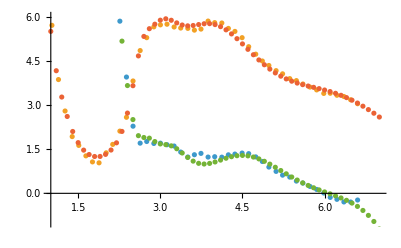

```mathematica
ListPlot[{auRe,auIm,hola1,hola2},PlotRange->{{1,7},{-1,6}}]
```

```mathematica
w0Bi={0,0.1,3.881,8.672,6.111,49.61,63.28,56.48,24.14,27.55,27.23,39.6,76.71};
fBi={0.4602,0.6222,0.2465,0.9131,0.1172,1.265,92.85,50.60,0.03968,0.04667,0.4006,76.34,1.858};
gBi={0.0011,0.1472,1.790,3.042,0.001,2.528,90.57,3.32,0.09824,0.001014,2.072,1.914,3.243};
sigmaBi={0,0.001026,0.1501,3.289,1.171,4.514,4.065,1.866,0.2423,0.5994,4.682,2.909,4.883};
wpBi=10;
```

```mathematica
hola3=Table[{w,-Re[epsTotOC[w,wpBi,gBi,fBi,w0Bi,sigmaBi,mu]]},{w,1,20,0.01}];
hola4=Table[{w,Im[epsTotOC[w,wpBi,gBi,fBi,w0Bi,sigmaBi,mu]]},{w,1,20,0.01}];
```

General::munfl: Exp[-384471.-63029.9 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-574974.-76994.7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4559.77+19.3756 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-384471.-63029.9 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-574974.-76994.7 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4559.77+19.3756 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
ListPlot[{hola3,hola4,bisRe,bisIm},PlotRange->{{0,6},{-2,6}}]
```

13

```mathematica
bi=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Congreso-2025\\Programas\\Werner.csv"];
nbi11=Drop[Drop[bi,{152,303}],1];
kbi11=Drop[bi,{1,153}];
nbi12=ToExpression[nbi11];
kbi12=ToExpression[kbi11];
wBi1=h vlight/(nbi12[[All,1]]*1000); (*λ en nm*)
nbi1=nbi12[[All,2]];
kBi1=kbi12[[All,2]];
nBi1=nbi1+ I kBi1;
epsBi=nBi1^2;
bisRe=Transpose[{wBi1,-Re[epsBi]}];
bisIm=Transpose[{wBi1,Im[epsBi]}];
```

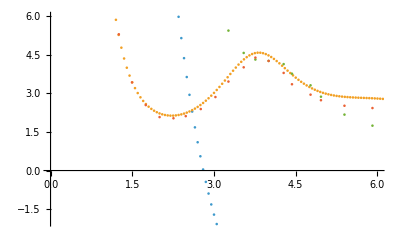

```mathematica
ListPlot[{hola3,hola4,bisRe,bisIm},PlotRange->{{0,6},{-2,6}}]
```

```mathematica
w0Ag={0,4.438,4.130,5.710,4.892,5.686,9.261};
fAg={1.053,0.03778,0.01484,0.1934,0.0713,0.01057,1.364};
gAg={0.02027,0.0001866,0.000001267,0.02518,0.3067,3.120,0.2362};
sigmaAg={0,0.2356,0.1424,0.7449,0.3309,3.070,1.998};
wpAg=8.9;
```

```mathematica
hola5=Table[{w,-Re[epsTotOC[w,wpAg,gAg,fAg,w0Ag,sigmaAg,mu]]},{w,1,7,0.05}];
hola6=Table[{w,Im[epsTotOC[w,wpAg,gAg,fAg,w0Ag,sigmaAg,mu]]},{w,1,7,0.05}];
```

```mathematica
ag=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Congreso-2025\\Programas\\Johnson Plata.csv"];
```

```mathematica
nag11=Drop[Drop[ag,{51,101}],1];
kag11=Drop[ag,{1,52}];
nag12=ToExpression[nag11];
kag12=ToExpression[kag11];
wAg1=h vlight/(nag12[[All,1]]*1000); (*λ en nm*)
nag1=nag12[[All,2]];
kAg1=kag12[[All,2]];
nAg1=nag1+ I kAg1;
epsAg=nAg1^2;
agRe=Transpose[{wAg1,-Re[epsAg]}];
agIm=Transpose[{wAg1,Im[epsAg]}];
```

```mathematica
ListPlot[{agRe,agIm},PlotRange->All]
```

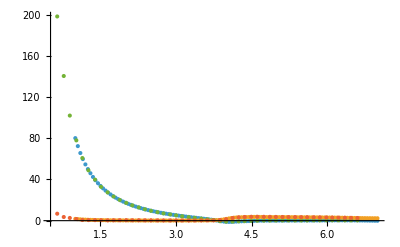

```mathematica
ListPlot[{hola5,hola6,agRe,agIm},PlotRange->All]
```

```mathematica
w0Al={0,1.762,1.529,1.465,2.886,0.4764};
fAl={0.7124,0.06685,0.02772,0.1401,0.05276,0.01236};
gAl={0.1007,0.6269,0.001109,1.191,1.749,0.3009};
sigmaAl={0,0.05226,0.1261,0.6698,1.144,0.0808};
wpAl=15.6;
hvFAl=2.03*10^(15)*hbar;
```

```mathematica
hola7=Table[{w,-Re[epsTotOC[w,wpAl,gAl,fAl,w0Al,sigmaAl,mu]]},{w,1.25,7,0.05}];
hola8=Table[{w,Im[epsTotOC[w,wpAl,gAl,fAl,w0Al,sigmaAl,mu]]},{w,1.25,7,0.05}];
```

General::munfl: Exp[-1684.47-340.053 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1739.28-346.189 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1795.05-352.287 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1684.47-340.053 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1739.28-346.189 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1795.05-352.287 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

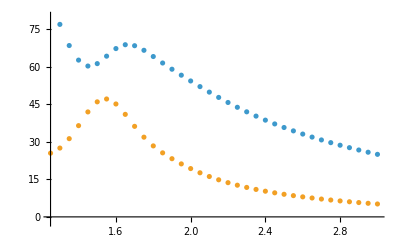

```mathematica
ListPlot[{hola7,hola8},PlotRange->{{1.25,3},{-2,80}}]
```

```mathematica
ag=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Congreso-2025\\Programas\\Johnson Plata.csv"];
```

```mathematica
nag11=Drop[Drop[ag,{51,101}],1];
kag11=Drop[ag,{1,52}];
nag12=ToExpression[nag11];
kag12=ToExpression[kag11];
wAg1=h vlight/(nag12[[All,1]]*1000); (*λ en nm*)
nag1=nag12[[All,2]];
kAg1=kag12[[All,2]];
nAg1=nag1+ I kAg1;
epsAg=nAg1^2;
agRe=Transpose[{wAg1,-Re[epsAg]}];
agIm=Transpose[{wAg1,Im[epsAg]}];
```

```mathematica
ListPlot[{agRe,agIm},PlotRange->All]
```

```mathematica
ListPlot[{hola5,hola6,agRe,agIm},PlotRange->All]
```